```mathematica
SetDirectory[NotebookDirectory[]];
```

## Line of sight

```mathematica
doublecapillary=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\stl files\\DC_500_500_90.STL","Graphics3D",ImageSize->960,ViewAngle->All,Lighting->Automatic,BaseStyle->RGBColor[0.7,0.8,0.86],ViewVertical->{1,1,0},ViewAngle->0.32,ViewPoint->{-0.3,1,0}];
```

```mathematica
Show[{doublecapillary,Graphics3D[{Arrowheads[{{.1,0.13},{.1,0.97}}],Red,Arrow[Tube[{{-20,18,502.5},{110,18,500}},0.3]]}]}]
```

-Graphics3D-

## Best result up to now

```mathematica
file="C:\\Users\\HILL\\Desktop\\ref.csv"
```

C:\Users\HILL\Desktop\ref.csv

```mathematica
data=Import["2020-12-30\\1.Wfm.csv","Table","FieldSeparators"->{";"}]
```

{{0,0.0869565,0.000365613},{-0.0395257,-0.150198,0.000365613},{-0.0395257,-0.0316206,0.000365613},{0,-0.0316206,0.000563241},{-0.0395257,-0.0316206,0.000365613},{-0.0395257,0.0869565,0.000167984},{-0.0395257,0.0869565,0.000167984},{0,0.0869565,0.000563241},4985,{-0.0395257,-0.387352,0.0064921},{0.0395257,-0.150198,0.00629447},{0,-0.268775,0.00688735},{0.0395257,-0.387352,0.00629447},{0,-0.268775,0.00668972},{0,-0.387352,0.00748024},{0.0395257,-0.150198,0.0064921}}
 |  |  |  |

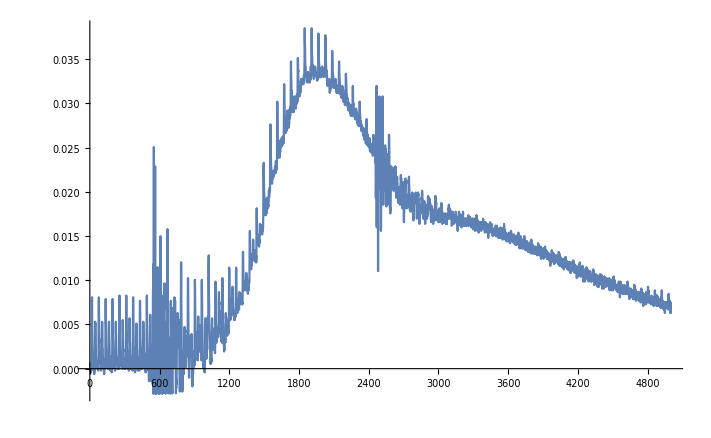

```mathematica
ListLinePlot[data[[All,3]],PlotRange->All]
```

```mathematica
Show[{doublecapillary,Graphics3D[{Red,Ball[{{77,18,500},{77,30,500},{77,18,520}}]}]},ViewVertical->{0.0742110583,0.99079208467,-0.11324205},ViewPoint->{0.7102,-0.044,-0.763922350}]
```

```mathematica
Show[{doublecapillary,Graphics3D[
{Gray,InfinitePlane[{{77,18,500},{77,30,500},{77,18,520}}]}]}
,ViewVertical->{0.0742110583,0.99079208467,-0.11324205},ViewPoint->{0.7102,-0.044,-0.763922350}]
```

-Graphics3D-